# Nakagami channel detection probability (switched m n comparison)

This notebook tests the accuracy of the switched m n approximate method against Annamalai’s exact method for cooperative networks of energy detectors operating on Nakagami-faded channels.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

27/06/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
<<definitions.m
<<plots.m
```

## Variables

Set the switching point to m n = 10:

```mathematica
switchingPoint=10;
```

Here, we define the ranges of values to be used for each parameter.

```mathematica
nRange={1,2,3,4,5,10,20};
mRange={0.5,1,1.5,2};
samplesRange={1000,10000,50000};
snrdbRange=Range[0,-21,-1];
snrRange=10^(snrdbRange/10);
pfRange={49/100,30/100,20/100,10/100,5/100,1/100,5/1000,1/1000,5/10000,1/10000,5/100000,1/100000};
```

Here, we select n and m so that m n ∈ I:

```mathematica
{nRange,mRange,mnRange}=Select[Flatten[Table[{nRange⟦i⟧,mRange⟦j⟧,nRange⟦i⟧ mRange⟦j⟧},{i,Length[nRange]},{j,Length[mRange]}],1],Ceiling[##[[3]]]==##[[3]]&]//Transpose;
```

## Calculations

Calculate the probability of detection, for each set of parameter values defined previously, using the exact and approximate methods:

```mathematica
exact=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Exact"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ExactAnnamalai",DatabaseLookup->True],{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

```mathematica
approx=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Approximate"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->{"ApproximateSwitchedMN",switchingPoint}]//N,{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

Calculate various error metrics:

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

## Results

### Detection probabilities

Plots of detection probabilities against signal to noise ratio, for the defined parameter sets, using the exact and approximate methods:

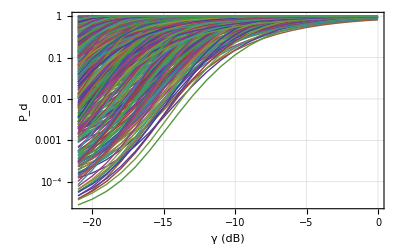
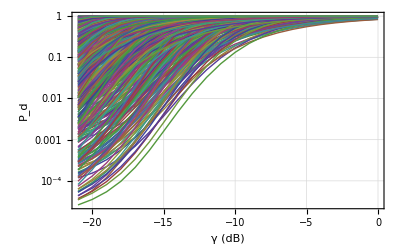

```mathematica
Table[CustomPlot[snrdbRange,y,{"γ (dB)","P_d"}],{y,{exact,approx}}]
```

### Error statistics

#### Error and absolute error

Probability density function of the approximation error:

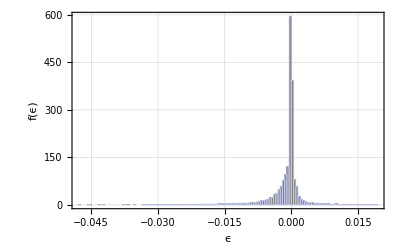

```mathematica
CustomHistogram[error,{"ϵ","f(ϵ)"}]
```

Histogram statistics:

```mathematica
StatsTable[error]
```

| μ | σ
 | -0.00125288 | 0.00469323

Largest errors:

```mathematica
MaxErrorsTable[absError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-10. | 5. | 2. | 1000. | 0.00001 | -0.0476604 | -0.0787824
-11. | 5. | 2. | 1000. | 0.00001 | -0.0456211 | -0.11941
-11. | 5. | 2. | 1000. | 0.00005 | -0.0450146 | -0.0947521
-11. | 5. | 2. | 1000. | 0.0001 | -0.04321 | -0.0832266
-12. | 10. | 1. | 1000. | 0.00001 | -0.042437 | -0.0844085
-12. | 10. | 1.5 | 1000. | 0.00001 | -0.0375558 | -0.0731205
-10. | 5. | 2. | 1000. | 0.00005 | -0.036717 | -0.0534894
-12. | 10. | 1. | 1000. | 0.00005 | -0.0366232 | -0.0618077
-12. | 10. | 2. | 1000. | 0.00001 | -0.0354071 | -0.0681165
-11. | 5. | 2. | 1000. | 0.0005 | -0.0352907 | -0.0561092

#### Relative error and absolute relative error

Probability density function of the relative approximation error:

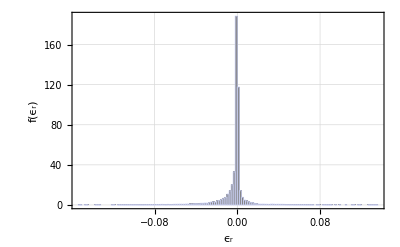

```mathematica
CustomHistogram[relError,{"ϵ_r","f(ϵ_r)"}]
```

Histogram statistics:

```mathematica
StatsTable[relError]
```

| μ | σ
 | -0.00301946 | 0.0151541

Largest relative errors:

```mathematica
MaxErrorsTable[absRelError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-12. | 1. | 2. | 1000. | 0.00001 | -0.00430786 | -0.152417
-11. | 1. | 2. | 1000. | 0.00001 | -0.00921272 | -0.151106
-14. | 1. | 1. | 1000. | 0.00001 | -0.00199287 | -0.146411
-13. | 1. | 1. | 1000. | 0.00001 | -0.00419473 | -0.14501
-10. | 1. | 2. | 1000. | 0.00001 | -0.0160096 | -0.137983
-13. | 1. | 2. | 1000. | 0.00001 | -0.0015787 | -0.135802
-16. | 5. | 2. | 1000. | 0.00001 | 0.000401421 | 0.135721
-12. | 1. | 1. | 1000. | 0.00001 | -0.00742539 | -0.134693
-15. | 1. | 1. | 1000. | 0.00001 | -0.000769386 | -0.133676
-17. | 5. | 2. | 1000. | 0.00001 | 0.000138392 | 0.13245